## Sulman & Gibert Modeling microbe munchers: Trophic interactions control global temperature response of soil carbon stocks Mathematica code

### EQUILIBRIA

```mathematica
Arr[T_,k_,Ea_,T0_]:=k*Exp[-Ea/(8.6*10^-5)(1/(273+T)-1/(273+T0))];
```

```mathematica
eqs2={S-Arr B c==0,
ϵ Arr B c-Subscript[α, P] Arr B P-d B==0,
Subscript[ϵ, P] Subscript[α, P] Arr B P-Subscript[d, P] P==0};
Solve[{S-Arr B c==0 ,
ϵ Arr B c-α1 Arr B P-d B==0 ,
ϵ2 α1 Arr B P-d2 P==0},{B,c,P}]
```

{{B→d2/(Arr α1 ϵ2),c→(S α1 ϵ2)/d2,P→(-d d2+Arr S α1 ϵ ϵ2)/(Arr d2 α1)},{B→(S ϵ)/d,c→d/(Arr ϵ),P→0}}

```mathematica
(* OLD, not needed *)
(*Solve[{S-(Arr1 B c)/(1+Arr1 η c)==0 ,
 ϵ(Arr1 B c)/(1+Arr1 η c)-(α1 Arr2 B P)/(1+α1 Arr2 η2 B)-d B==0 , 
 ϵ2(α2 Arr2 B P)/(1+α2 Arr2 η2 B)-δ P==0},{B,c,P}]*)
```

{{B→(S ϵ)/d,c→d/(Arr1 (ϵ-d η)),P→0},{B→δ/(Arr2 α2 (ϵ2-δ η2)),c→-(-Arr2 S α2 ϵ2+Arr2 S α2 δ η2)/(Arr1 (δ-Arr2 S α2 ϵ2 η+Arr2 S α2 δ η η2)),P→((α2 ϵ2+α1 δ η2-α2 δ η2) (-d δ+Arr2 S α2 ϵ ϵ2-Arr2 S α2 δ ϵ η2))/(Arr2 α1 α2 δ (ϵ2-δ η2))}}

```mathematica
Solve[{S-(Arr1 B c)/(1+Arr1 η c)==0 ,
 ϵ(α1 Arr1 B c)/(1+α1 Arr1 η c)-(α2 Arr2 B P)/(1+α2 Arr2 η2 B)-d B==0 , 
 ϵ2(α2 Arr2 B P)/(1+α2 Arr2 η2 B)-δ P==0},{B,c,P}]
```

{{B→(S α1 ϵ+d S η-d S α1 η)/d,c→d/(Arr1 α1 (ϵ-d η)),P→0},{B→δ/(Arr2 α2 (ϵ2-δ η2)),c→-(-Arr2 S α2 ϵ2+Arr2 S α2 δ η2)/(Arr1 (δ-Arr2 S α2 ϵ2 η+Arr2 S α2 δ η η2)),P→-(ϵ2 (d δ-Arr2 S α1 α2 ϵ ϵ2-Arr2 d S α2 ϵ2 η+Arr2 d S α1 α2 ϵ2 η+Arr2 S α1 α2 δ ϵ η2+Arr2 d S α2 δ η η2-Arr2 d S α1 α2 δ η η2))/(Arr2 α2 (ϵ2-δ η2) (δ-Arr2 S α2 ϵ2 η+Arr2 S α1 α2 ϵ2 η+Arr2 S α2 δ η η2-Arr2 S α1 α2 δ η η2))}}

### FIGURE 2 of main text

```mathematica
(* Equations *)
Arr[T_,k_,Ea_,T0_]:=k*Exp[-Ea/(8.6*10^-5)(1/(273+T)-1/(273+T0))];
eqs={S-(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)==0,
ϵ(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)-(Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B)-d B==0,
Subscript[ϵ, P]((Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B))-Subscript[d, P] P==0};;
eqs2={S-(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)==0,
ϵ(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)-(Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B)-d B==0,
Subscript[ϵ, P]((Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B))-Subscript[d, P] P==0};
```

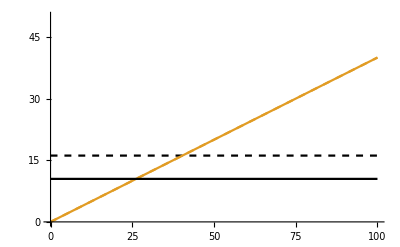

```mathematica
(* Figure 1: PLOTS *)
Plot[{(S ϵ)/d/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0},d/(Arr[T,k,Ea,T0](ϵ-d η))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0},(S ϵ)/d/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0},d/(Arr[T,k,Ea,T0](ϵ-d η))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0}},{S,0,100},PlotRange->{0,50},AxesStyle->Thickness[0.003], Ticks->{{0,25,50,75,100},{0,15,30,45,60}},PlotStyle->{{ColorData[97,"ColorList"][[2]],Dashed},{Black,Dashed},ColorData[97,"ColorList"][[2]],Black}, TicksStyle->Directive[12]]
```

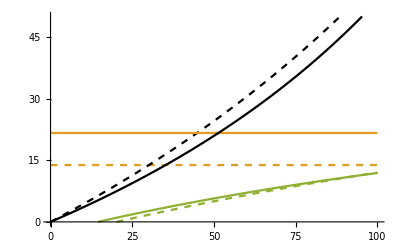

```mathematica
Plot[{δ/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.65},-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.65},-(ϵ2 (d δ-Arr[T,k,Ea2,T0] S α1 α2 ϵ ϵ2-Arr[T,k,Ea2,T0] d S α2 ϵ2 η+Arr[T,k,Ea2,T0] d S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 δ ϵ η2+Arr[T,k,Ea2,T0] d S α2 δ η η2-Arr[T,k,Ea2,T0] d S α1 α2 δ η η2))/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2) (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2-Arr[T,k,Ea2,T0] S α1 α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.5},δ/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0},-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.5},-(ϵ2 (d δ-Arr[T,k,Ea2,T0] S α1 α2 ϵ ϵ2-Arr[T,k,Ea2,T0] d S α2 ϵ2 η+Arr[T,k,Ea2,T0] d S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 δ ϵ η2+Arr[T,k,Ea2,T0] d S α2 δ η η2-Arr[T,k,Ea2,T0] d S α1 α2 δ η η2))/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2) (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2-Arr[T,k,Ea2,T0] S α1 α2 δ η η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.5}},{S,0,100},PlotRange->{0,50},AxesStyle->Thickness[0.003], Ticks->{{0,25,50,75,100},{0,15,30,45,60}},PlotStyle->{{ColorData[97,"ColorList"][[2]],Dashed},{Black,Dashed},{ColorData[97,"ColorList"][[3]],Dashed},ColorData[97,"ColorList"][[2]],Black,ColorData[97,"ColorList"][[3]]}, TicksStyle->Directive[12]]
```

### FIGURE 3 of the main text

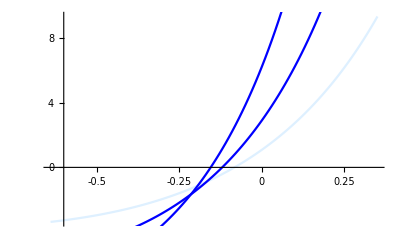

```mathematica
Act=Array[0+0.01# &,100];
(* Against Substrate [not included in the paper] *)
toPlot40=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->24,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->40})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->40})
,{i,Length[Act]}];
toPlot60=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->24,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
toPlot80=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->24,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->80})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->80})
,{i,Length[Act]}];
Plot40=ListLinePlot[Transpose[{Act-0.65,toPlot40}],AxesOrigin->{-0.6,0},PlotStyle->LightBlue,AxesStyle->Thickness[0.003], Ticks->{{-0.5,-0.25,0,0.25},{-4,0,4,8}}, TicksStyle->Directive[12]];
Plot60=ListLinePlot[Transpose[{Act-0.65,toPlot60}],AxesOrigin->{-0.6,0},PlotStyle->Blue];
Plot80=ListLinePlot[Transpose[{Act-0.65,toPlot80}],AxesOrigin->{-0.6,0},PlotStyle->Blue];
Show[Plot40,Plot60,Plot80]
```

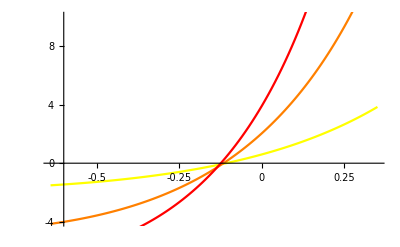

```mathematica
(* Against Substrate [not included in the paper] *)
toPlot21=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->21,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
toPlot23=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->23,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
toPlot25=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
Plot21=ListLinePlot[Transpose[{Act-0.65,toPlot21}],AxesOrigin->{-0.6,0},PlotStyle-> Yellow,AxesStyle->Thickness[0.003], Ticks->{{-0.5,-0.25,0,0.25},{-4,0,4,8}},PlotRange->{-4,10}, TicksStyle->Directive[12]];
Plot23=ListLinePlot[Transpose[{Act-0.65,toPlot23}],AxesOrigin->{-0.6,0},PlotStyle->Orange];
Plot25=ListLinePlot[Transpose[{Act-0.65,toPlot25}],AxesOrigin->{-0.6,0},PlotStyle->Red];
Show[Plot21,Plot23,Plot25]
```